# Mallinckrodt Functions

## Precipitation Background

```mathematica
eV2mJ=1.60218 10^-19 10^3(*mJ/eV*);
ϕM[EE_,Q0_,E0_]:=Q0/(2 E0^3)EE Exp[-EE/E0]
LogLogPlot[ϕM[EE,1.3 10^12,1000],{EE,2 10^2,4 10^4},PlotRange->{{2 10^2,4 10^4},{10^3,10^6}}]
```

```mathematica
Q0BG=1.3 10^12 eV2mJ 100^2(*mW m^-2*)
E0BG=1000(*eV*)
```

## Precipitation Arc

```mathematica
line[E_,x1_,x2_,y1_,y2_]:=Module[{b,bb,bbb,a,aa},
bb=Solve[Log10[y1]==Log10[a]+b Log10[x1],b][[1,1,2]];
aa=Solve[Log10[y2]==Log10[a]+bb Log10[x2],a][[1,1,2]];
bbb=bb/.a->aa;
aa E^bbb
]
spectrum=Piecewise[{
{line[EE,2 10^2,6 10^2,1 10^5,3 10^4],2 10^2≤ EE<6 10^2}
,{line[EE,6 10^2,8 10^3,3 10^4,2 10^5],6 10^2≤ EE<8 10^3}
,{line[EE,8 10^3,8.2 10^3,2 10^5,5 10^5],8 10^3≤ EE<8.2 10^3}
,{line[EE,8.2 10^3,9 10^3,5 10^5,9 10^5],8.2 10^3≤ EE<9 10^3}
,{line[EE,9 10^3,1.1 10^4,9 10^5,5 10^5],9 10^3≤ EE<1.1 10^4}
,{line[EE,1.1 10^4,2 10^4,5 10^5,2 10^3],1.1 10^4≤ EE<2 10^4}
},0];
LogLogPlot[spectrum,{EE,2 10^2,4 10^4},PlotRange->{{2 10^2,4 10^4},{10^3,10^6}},ImageSize->Large]
```

```mathematica
II=Integrate[spectrum,{EE,0,∞}];
E0ARC=8000;(*eV*)
Q0ARC=Solve[II==Q0/(2(8000)),Q0][[1,1,2]]eV2mJ 100^2(*eV*)
```

## Grid

```mathematica
Plot[4000+3600*Tanh[((alt-230000)/36000)],{alt,80000,260000},GridLines->All]
```

```mathematica
Plot[d2+d3*(1+Tanh[((X-ydist/2+d1)/d4)])/2/.{d1->30000,d2->250,d3->1000,d4->6000,ydist->120000},{X,-60000,60000},PlotRange->All]
```

## Functions

```mathematica
sheet[x_,p_,w_,g_]:=(Tanh[2(x-p+w/2)/g]-Tanh[2(x-p-w/2)/g])/2
j1[X_]:=(0.25-3.1sheet[X,15000,24000,10000])10^-6
j[X_]:=2.9 10^-6(sheet[X,-15000,24000,10000]-sheet[X,15000,24000,10000])
E3[X_]:=(80-45sheet[X,15000,19000,8000])10^-3
Q[X_]:=90sheet[X,15000,15000,9000]
E0[X_]:=1000+7000sheet[X,15000,15000,9000]
Plot[{j[X],j1[X]},{X,-32000,32000},PlotRange->{{-30000,30000},{3,-3}10^-6},GridLines->All,AspectRatio->1/2]
Plot[E3[X],{X,-32000,32000},PlotRange->{{-30000,30000},{0,80}10^-3},GridLines->All,AspectRatio->1/2]
Plot[Q[X],{X,-32000,32000},PlotRange->{{-30000,30000},{-5,100}},GridLines->All,AspectRatio->1/2]
Plot[E0[X],{X,-32000,32000},PlotRange->{{-30000,30000},{-1000,9000}},GridLines->All,AspectRatio->1/2]
```

## Predictions

```mathematica
Manipulate[
ΣP=8+(35-8)sheet[X,15000,ws,gs];
EE3=(80-45sheet[X,15000,we,ge])10^-3;
jpar=-10^6 D[ΣP EE3,X];
Plot[jpar,{X,0,30000},PlotRange->{{0,30000},{-90,60}}]
,{{ws,15000},10000,20000}
,{{gs,9000},1000,10000}
,{{we,19000},10000,30000}
,{{ge,8000},1000,10000}
]
```

```mathematica
Manipulate[
ΣP=8+(35-8)sheet[X,15000,ws,gs];
jpar=(0.25-3.1sheet[X,15000,24000,10000])10^-6;
EE3=Integrate[jpar,X]/ΣP;
Plot[1000EE3,{X,0,30000},PlotRange->{{0,30000},{-5,5}}]
,{{ws,15000},10000,20000}
,{{gs,9000},1000,10000}
,{{we,19000},10000,30000}
,{{ge,8000},1000,10000}
]
```

## Imports

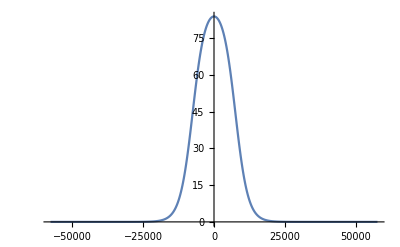

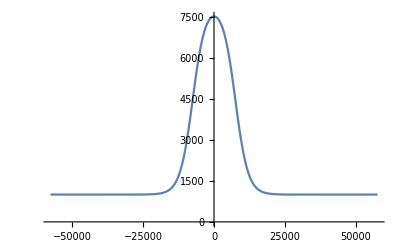

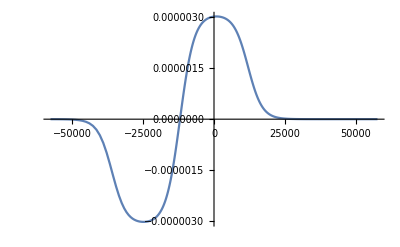

```mathematica
t=36000;
run="09";
dir="\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\";
dir="D:\\Files\\research\\thesis\\";
x3=Import[dir<>"mallinckrodt_"<>run<>"\\inputs\\simgrid.h5","/x3"][[3;;-3]];
dx3=Import[dir<>"\\mallinckrodt_"<>run<>"\\inputs\\simgrid.h5","/dx3h"];
Qp=Import[dir<>"mallinckrodt_"<>run<>"\\inputs\\particles\\20150201_"<>ToString[t]<>".000000.h5","/Qp"]//Flatten;
E0p=Import[dir<>"mallinckrodt_"<>run<>"\\inputs\\particles\\20150201_"<>ToString[t]<>".000000.h5","/E0p"]//Flatten;
Vmaxx1it=Import[dir<>"mallinckrodt_"<>run<>"\\inputs\\fields\\20150201_"<>ToString[t]<>".000000.h5","/Vmaxx1it"]//Flatten;
ListLinePlot[Transpose[{x3,Qp}]]
ListLinePlot[Transpose[{x3,E0p}]]
ListLinePlot[Transpose[{x3,Vmaxx1it}]]
```

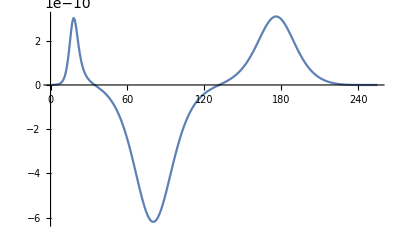

```mathematica
ListLinePlot[-Differences[Vmaxx1it]/dx3[[1;;-2]]]
```

```mathematica
t=35860;
run="10";
dir="\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\";
(*dir="D:\\Files\\research\\thesis\\";*)
x1=Import[dir<>"mallinckrodt_"<>run<>"\\inputs\\simgrid.h5","/x1"][[3;;-3]];
x3=Import[dir<>"mallinckrodt_"<>run<>"\\inputs\\simgrid.h5","/x3"][[3;;-3]];
J1all=Flatten[Import[dir<>"mallinckrodt_"<>run<>"\\20150201_"<>ToString[t]<>".000000.h5","/J1all"],1];
J2all=Flatten[Import[dir<>"mallinckrodt_"<>run<>"\\20150201_"<>ToString[t]<>".000000.h5","/J2all"],1];
J3all=Flatten[Import[dir<>"mallinckrodt_"<>run<>"\\20150201_"<>ToString[t]<>".000000.h5","/J3all"],1];
Phiall=Import[dir<>"mallinckrodt_"<>run<>"\\20150201_"<>ToString[t]<>".000000.h5","/Phiall"]//Flatten;
vecs=Table[{{x3[[i]]/1000+22,x1[[j]]/1000},{J3all[[i,j]],J1all[[i,j]]}},{i,1+0 32,237},{j,1,256}];
j2dens=Table[{x3[[i]]/1000,x1[[j]]/1000,J2all[[i,j]]},{i,1,256},{j,1,256}];
```

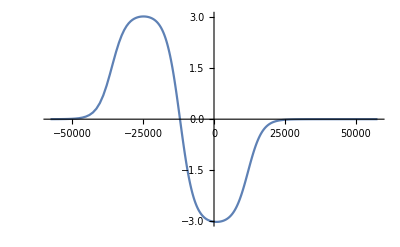

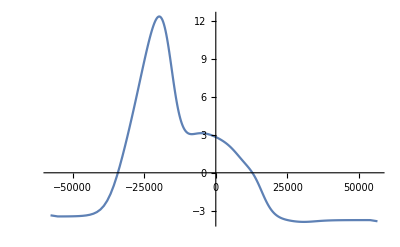

```mathematica
ListLinePlot[Transpose[{x3,-10^6 J1all[[;;,-1]]}]]
ListLinePlot[Transpose[{x3[[1;;-2]],-1000Differences[Phiall]/dx3[[1;;-2]]}]]
```

```mathematica
Max[J2all] 10^6
```

14.8677

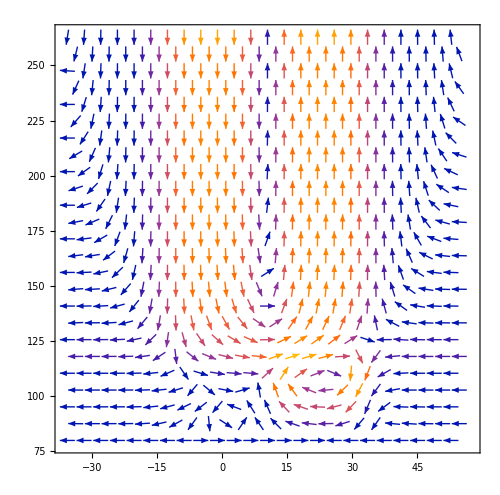

```mathematica
ar=MinMax[Flatten[vecs[[;;,;;,1,2]]]].{-1,1}/MinMax[Flatten[vecs[[;;,;;,1,1]]]].{-1,1};
ListVectorPlot[Flatten[vecs,1],ImageSize->500,PlotLegends->Automatic,VectorPoints->Fine,AspectRatio->ar/2]
```

```mathematica
ListStreamPlot[Flatten[vecs,1],ImageSize->Large,PlotLegends->Automatic,StreamPoints->Fine,AspectRatio->ar/2]
```

## 3D Case

```mathematica
t=35900;
run="01";
x1=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\mallinckrodt_3D_"<>run<>"\\inputs\\simgrid.h5","/x1"][[3;;-3]];
x3=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\mallinckrodt_3D_"<>run<>"\\inputs\\simgrid.h5","/x3"][[3;;-3]];
J1all=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\mallinckrodt_3D_"<>run<>"\\20150201_"<>ToString[t]<>".000000.h5","/J1all"];
J2all=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\mallinckrodt_3D_"<>run<>"\\20150201_"<>ToString[t]<>".000000.h5","/J2all"];
J3all=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\mallinckrodt_3D_"<>run<>"\\20150201_"<>ToString[t]<>".000000.h5","/J3all"];
```

```mathematica
vecs=Table[{{x3[[i]]/1000+22,x1[[j]]/1000},{J3all[[i,32,j]],J1all[[i,32,j]]}},{i,32,237},{j,1,256}];
```

```mathematica
ar=MinMax[Flatten[vecs[[;;,;;,1,2]]]].{-1,1}/MinMax[Flatten[vecs[[;;,;;,1,1]]]].{-1,1};
ListVectorPlot[Flatten[vecs,1],ImageSize->500,PlotLegends->Automatic,VectorPoints->Fine,AspectRatio->ar/2]
```

```mathematica
ListStreamPlot[Flatten[vecs,1],ImageSize->Large,PlotLegends->Automatic,StreamPoints->Fine,AspectRatio->ar/2]
```

## OTHER

```mathematica
MinMax@Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\Jules\\initial_conditions\\mallinckrodt_ic_03\\20150201_35850.000000.h5","/nsall"][[2]]//Flatten
```

```mathematica
d=256 64
```

```mathematica
d/Range[32,64]
```

```mathematica
run="aurora_sharc_01";
(*run="aurora_null_02";*)
Qp=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\particles\\20150201_36000.000000.h5","/Qp"];
E0p=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\particles\\20150201_36000.000000.h5","/E0p"];
Vmaxx1it=Import["\\\\Dartfs-hpc\\rc\\lab\\L\\LynchK\\public_html\\Gemini3D\\"<>run<>"\\inputs\\fields\\20150201_36000.000000.h5","/Vmaxx1it"];
```

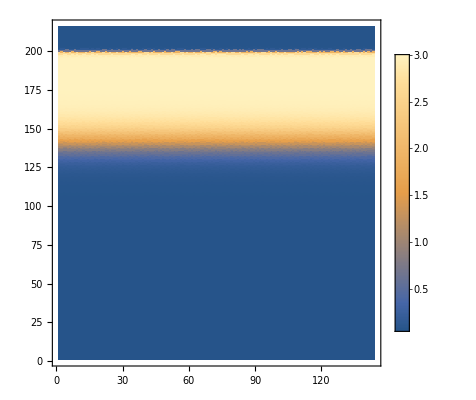

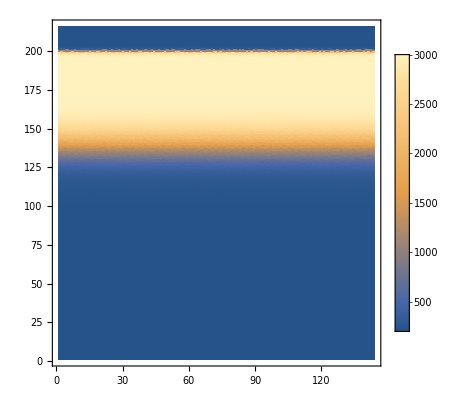

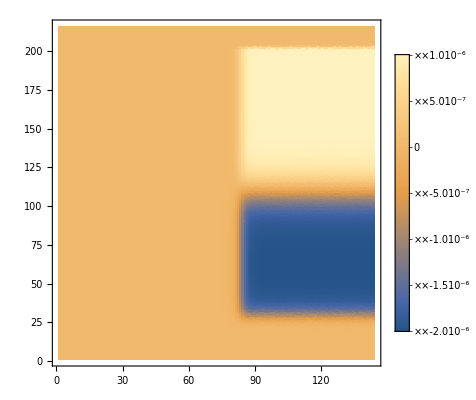

```mathematica
ListDensityPlot[Qp,InterpolationOrder->0,PlotRange->All,PlotLegends->Automatic]
ListDensityPlot[E0p,InterpolationOrder->0,PlotRange->All,PlotLegends->Automatic]
ListDensityPlot[Vmaxx1it,InterpolationOrder->0,PlotRange->All,PlotLegends->Automatic]
```